```mathematica
data=Import["C:\\Users\\PC\\Documents\\GitHub\\QMLTests\\experimental_data_QSVC.csv"]
```

{{,0},{0,0.8},{1,0.8},{2,1.},{3,1.},{4,1.},{5,1.},{6,1.},{7,1.},{8,1.},{9,1.},{10,0.85},{11,0.85},{12,0.9},{13,0.9},{14,0.9},{15,0.9},{16,1.},{17,1.},{18,0.9},{19,0.9},{20,0.9},{21,0.9},{22,0.8},{23,0.8},{24,0.9},{25,0.9},{26,0.85},{27,0.85},{28,0.9},{29,0.9},{30,0.85},{31,0.85},{32,1.},{33,1.},{34,0.9},{35,0.9},{36,0.85},{37,0.85},{38,1.},{39,1.},{40,1.},{41,1.},{42,0.7},{43,0.7},{44,1.},{45,1.},{46,0.8},{47,0.8},{48,1.},{49,1.},{50,0.95},{51,0.95},{52,0.9},{53,0.9}}

```mathematica
(*Reading data*)
```

```mathematica
data[[2;;,;;]]
```

{{0,0.8},{1,0.8},{2,1.},{3,1.},{4,1.},{5,1.},{6,1.},{7,1.},{8,1.},{9,1.},{10,0.85},{11,0.85},{12,0.9},{13,0.9},{14,0.9},{15,0.9},{16,1.},{17,1.},{18,0.9},{19,0.9},{20,0.9},{21,0.9},{22,0.8},{23,0.8},{24,0.9},{25,0.9},{26,0.85},{27,0.85},{28,0.9},{29,0.9},{30,0.85},{31,0.85},{32,1.},{33,1.},{34,0.9},{35,0.9},{36,0.85},{37,0.85},{38,1.},{39,1.},{40,1.},{41,1.},{42,0.7},{43,0.7},{44,1.},{45,1.},{46,0.8},{47,0.8},{48,1.},{49,1.},{50,0.95},{51,0.95},{52,0.9},{53,0.9}}

```mathematica
nnoise=Table[data⟦i⟧[[2]],{i,1,Length[data],2}][[2;;]];
noise=Table[data⟦i⟧[[2]],{i,2,Length[data],2}][[2;;]];
```

```mathematica
nnoise
```

{0.8,1.,1.,1.,1.,0.85,0.9,0.9,1.,0.9,0.9,0.8,0.9,0.85,0.9,0.85,1.,0.9,0.85,1.,1.,0.7,1.,0.8,1.,0.95,0.9}

```mathematica
nnoise
```

{0.8,1.,1.,1.,1.,0.85,0.9,0.9,1.,0.9,0.9,0.8,0.9,0.85,0.9,0.85,1.,0.9,0.85,1.,1.,0.7,1.,0.8,1.,0.95,0.9}

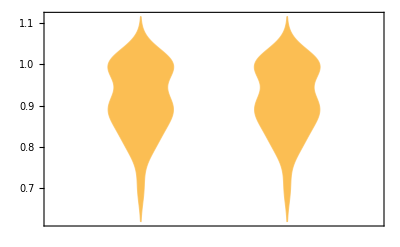

```mathematica
Show[DistributionChart@{nnoise,nnoise}]
```

```mathematica
α=1-KolmogorovSmirnovTest[noise,nnoise]
```

0.

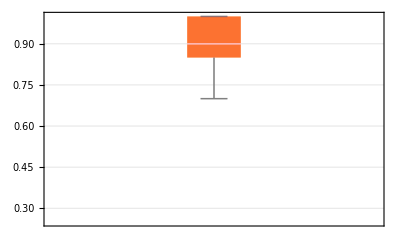

```mathematica
Show[{{BoxWhiskerChart[nnoise[[2;;]]ᵀ, ChartLabels->nnoise[[1,;;]],PlotTheme->"Detailed",PlotRange->{0.25,1},ChartLabels->{"No Noise"}]},{BoxWhiskerChart[noise[[2;;]]ᵀ, ChartLabels->nnoise[[1,;;]],PlotTheme->"Detailed",PlotRange->{0.25,1},ChartStyle->{Opacity[0.4],{Red,Red,Red},ChartLabels->{"Noise"}}]}}ᵀ]
```

```mathematica
With[
{x=noise[[2;;]],
y=nnoise[[2;;]]},
KolmogorovSmirnovTest[x,y,"TestDataTable"]]
```

| Statistic | P-Value
Kolmogorov-Smirnov | 0.0246154 | 1.

```mathematica
PairedHistogram[nnoise[[2;;]],noise[[2;;]],8, PlotTheme->"Detailed"]
```

-Graphics-

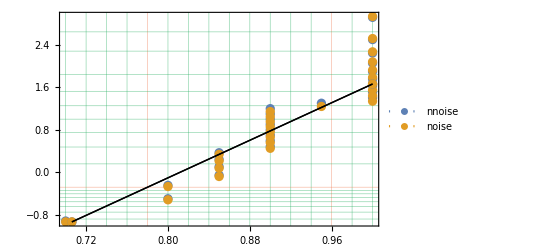

```mathematica
ProbabilityScalePlot[{noise[[2;;]],nnoise[[2;;]]},PlotLegends->{"nnoise","noise"}, GridLines->Automatic, GridLinesStyle->"Classic",PlotRange->Full]
```

```mathematica
Table[((2π-i)/(2π))*100//N,{i,0,1,0.1}]
```

{100.,98.4085,96.8169,95.2254,93.6338,92.0423,90.4507,88.8592,87.2676,85.6761,84.0845}

```mathematica
100-%
```

{0.,1.59155,3.1831,4.77465,6.3662,7.95775,9.5493,11.1408,12.7324,14.3239,15.9155}